```mathematica
deq=D[Y[x,t],t]-𝒟 D[Y[x,t],{x,2}]==0
```

Y^(0,1)[x,t]-𝒟 Y^(2,0)[x,t]==0

```mathematica
f0[t_]:=t
```

```mathematica
f1[t_]:=0
```

```mathematica
g0[x_]:=0
```

```mathematica
sol=DSolve[{
deq,
Y[0,t]==f0[t],
Y[1,t]==f1[t],
Y[x,0]==g0[x]},
Y[x,t],{x,t}]
```

{{Y[x,t]→t-t x+-((2-2 ⅇ^(-π^2 t 𝒟 K[1]^2)) Sin[π x K[1]])/(π^3 K[1]^3)K[1]1∞}}

```mathematica
Yf[x_,t_]:=Y[x,t]/.sol[[1]]
```

```mathematica
Yf[x_,t_,𝒟_]:=t(1-x)-∑_(k=1)^20 (2(1-ⅇ^(-π^2 t 𝒟 k^2))Sin[π x k])/(π^3 k^3)
```

```mathematica
𝒟=1
```

1

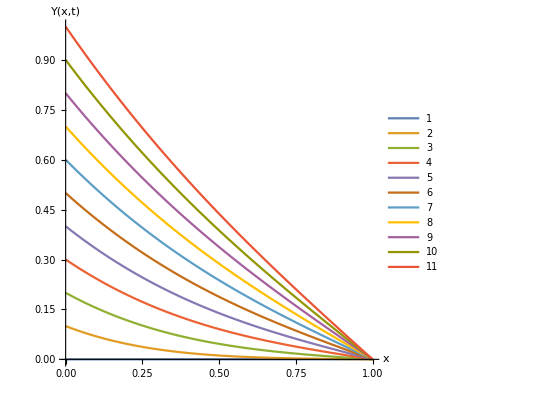

```mathematica
Plot[{Yf[x,0,𝒟],Yf[x,0.1,𝒟],Yf[x,0.2,𝒟],Yf[x,0.3,𝒟],Yf[x,0.4,𝒟],Yf[x,0.5,𝒟],Yf[x,0.6,𝒟],Yf[x,0.7,𝒟],Yf[x,0.8,𝒟],Yf[x,0.9,𝒟],Yf[x,1.0,𝒟]},{x,0,1},PlotRange->{0,1},AxesLabel->{"x","Y(x,t)"},PlotLegends->Automatic,AspectRatio->1]
```

```mathematica
Yf[0,0,1]
```

0